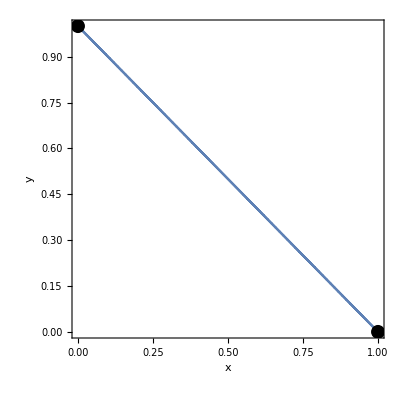

F:\Univ\_PhD\TA\MATH0462\Syllabus\2_2_not.pdf

```mathematica
p=RegionPlot[y==1-x,{x,0,1},{y,0,1},
FrameLabel->{Text@Style["x",FontSize->20],Text@Style["y",FontSize->20]},
Epilog->{
PointSize[.025],
Point[{{0,1},{1 ,0}}]
}
]
Export[NotebookDirectory[]<>"2_2_not.pdf",p]
```